```mathematica
ClearAll[p,vm]
D[D[Log[p(1-p)/(1/y-vm+p(1-p)-1/2)],y],y]
```

1/((-1/2+(1-p) p-vm+1/y)^2 y^4)-2/((-1/2+(1-p) p-vm+1/y) y^3)

```mathematica
Solve[1/((-1/2+(1-p) p-vm+1/y)^2 y^4)-2/((-1/2+(1-p) p-vm+1/y) y^3)==0,y]
```

{{y→1/(1-2 p+2 p^2+2 vm)}}

```mathematica
Simplify[1/((-19/2+1/y)^2 y^4)-2/((-19/2+1/y) y^3)]
```

(-4+76 y)/((2-19 y)^2 y^2)

```mathematica
p=0.1;
vm=9;
(8 (-1+p) p (1+2 vm))/(-2+y+2 vm y)^3
```

-13.68/(-2+19 y)^3

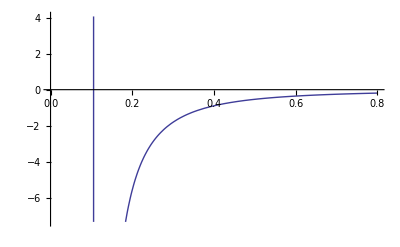

```mathematica
Plot[0.9999999999999999/((-19/2+1/y) y^2),{y,0,0.8}]
```

```mathematica
D[Log[p(1-p)/(1/y-vm-1/2)],y]
```

1./((-19/2+1/y) y^2)

```mathematica
vm=9;
p=0.1;
1/(1-2 p+2 p^2+2 vm)
```

0.053135

```mathematica
p=0.5;
α[p]=Table[{0.005+i*0.0005,p(1-p)/(1/(0.005+i*0.0005)-9+p(1-p)-0.5)},{i,0,185}];
```

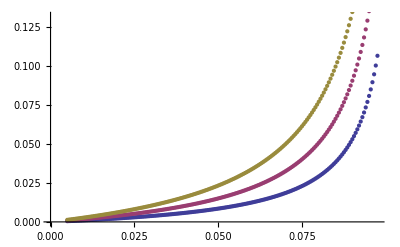

```mathematica
ListPlot[{α[0.1],α[0.2],α[0.5]}]
```

((1-p) p)/((-1/2+(1-p) p-vm+1/y)^2 y^2)

(2 (1-p) p)/((-1/2+(1-p) p-vm+1/y)^3 y^4)-(2 (1-p) p)/((-1/2+(1-p) p-vm+1/y)^2 y^3)

0.09/((-9.41+1/y)^2 y^2)

0.18/((-9.41+1/y)^3 y^4)-0.18/((-9.41+1/y)^2 y^3)

0.54/((-9.41+1/y)^4 y^6)-1.08/((-9.41+1/y)^3 y^5)+0.54/((-9.41+1/y)^2 y^4)

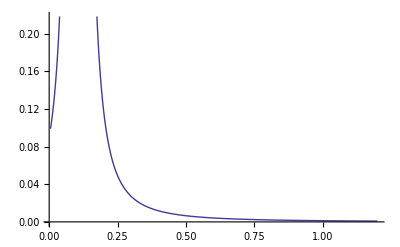

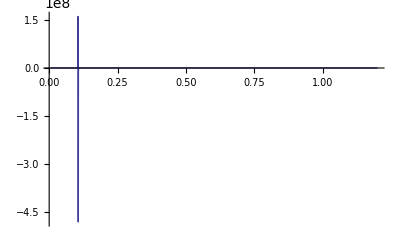

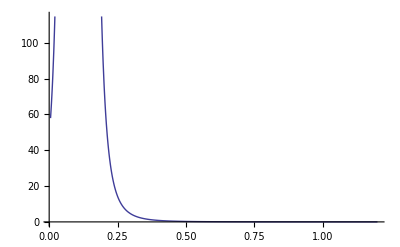

```mathematica
ClearAll[vm,p]
D[p(1-p)/(1/y-vm+p(1-p)-1/2),y]
D[D[p(1-p)/(1/y-vm+p(1-p)-1/2),y],y]
p=0.1;
vm=9;
D[p(1-p)/(1/y-vm+p(1-p)-1/2),y]
D[D[p(1-p)/(1/y-vm+p(1-p)-1/2),y],y]
D[D[D[p(1-p)/(1/y-vm+p(1-p)-1/2),y],y],y]
Plot[0.09000000000000001/((-9.41+1/y)^2 y^2),{y,0.005,1.2}]
Plot[0.18000000000000002/((-9.41+1/y)^3 y^4)-0.18000000000000002/((-9.41+1/y)^2 y^3),{y,0.005,1.2},PlotRange->Full]
Plot[0.54/((-9.41+1/y)^4 y^6)-1.08/((-9.41+1/y)^3 y^5)+0.54/((-9.41+1/y)^2 y^4),{y,0.005,1.2}]
```